```mathematica
sol = NDEigensystem[{-Laplacian[f[x],{x}]+x^4 f[x], DirichletCondition[f[x]==0,True]},f[x],{x,-100,100},4]
```

{{38.5378,920.283,1139.14,11252.},{InterpolatingFunction[…][x],InterpolatingFunction[…][x],InterpolatingFunction[…][x],InterpolatingFunction[…][x]}}

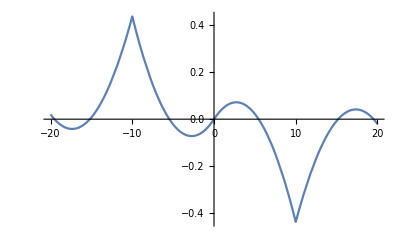

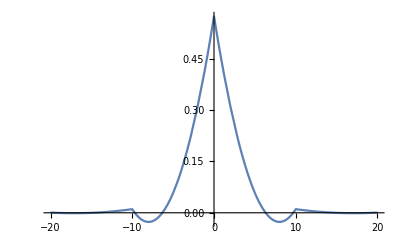

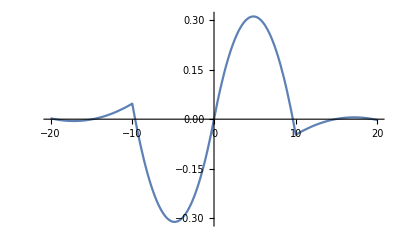

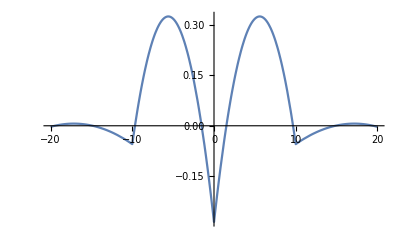

```mathematica
Plot[sol[[2,4]],{x,-20,20},PlotRange->All]
Plot[sol[[2,1]],{x,-20,20},PlotRange->All]
Plot[sol[[2,2]],{x,-20,20},PlotRange->All]
Plot[sol[[2,3]],{x,-20,20},PlotRange->All]
```